# Лабораторная работа № 1. Базовые методики вычислений.

Выполнила студентка ММФ БГУ 
КМ, 1 к, 5 гр. Бельская Е.А.
  2 сентября 2019

## 1. Вычислите с точностью до 11 знаков после запятой значения трёх сложных математических выражений. Выражения выберите самостоятельно.

Используйте функции базового математического пакета. Доступ к записи типичных математических выражений осуществляется через меню Palettes ->  Basic Math Assistant. Используйте также комбинации горячих клавиш.

```mathematica
expr=(Cos[√96+(√65)/(√(5789^(1/4)))]+Tan[69])/(Sin[36]+56^(5/6))
```

(Cos[4 √6+(√65)/5789^(1/8)]+Tan[69])/(4 √2 7^(5/6)+Sin[36])

```mathematica
N[expr,11]
```

0.031973909566

```mathematica
expr1=((Sin[32]^2+Log10[(√69)/6])/(√574+Tan[10^(41/54)]))^(1/(1/3))
```

((Log[(√(23/3))/2]/Log[10]+Sin[32]^2)^3)/((√574+Tan[10^(41/54)])^3)

```mathematica
N[expr1, 11]
```

6.9283022836×10^-6

```mathematica
expr2=Sin[3]^(9/((√(Log[63]×6^8))/(Cos[65]+Tan[25])))
```

Sin[3]^((Cos[65]+Tan[25])/(144 √Log[63]))

```mathematica
N[expr2,11]
```

1.0046604162

## 2. Постройте графики следующих функций (согласно вариантам).

### 2.1

y=1/(x+√x)

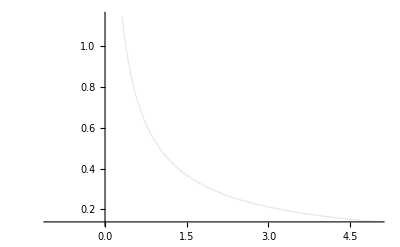

```mathematica
Plot[1/(x+√x),{x,-1,5},PlotStyle->{LightBrown,Thin}, ExclusionsStyle->Red]
```

y = sin (x) + cos (2 x)

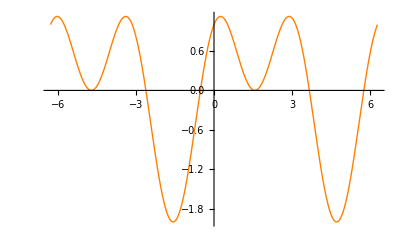

```mathematica
Plot[Sin[x]+Cos[2x],{x,-2π,2π}, PlotStyle->{Orange,Thick}]
```

y=(x^7+2x+1)/(x^23-4x+3)

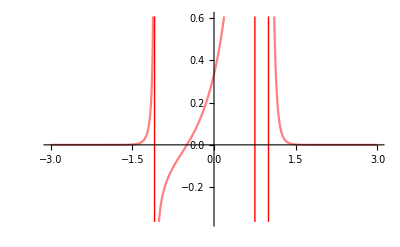

```mathematica
Plot[(x^7+2x+1)/(x^23-4x+3), {x,-3,3},PlotStyle->Pink, ExclusionsStyle->Red]
```

y = n!

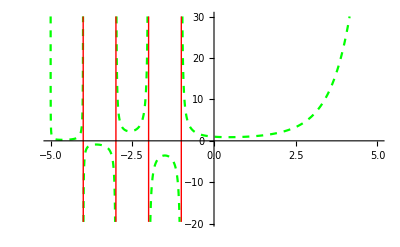

```mathematica
Plot[x!, {x,-5,5}, PlotStyle->{Green, Dashed}, ExclusionsStyle->Red]
```

#### 2.2-2.4

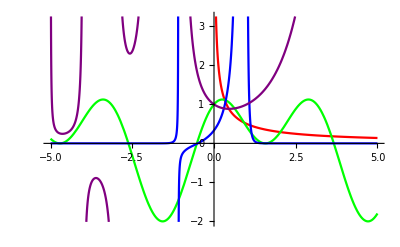

```mathematica
Plot[{1/(x+√x), Sin[x]+Cos[2x],(x^7+2x+1)/(x^23-4x+3), x!},{x,-5,5}, PlotStyle->{Red, Green, Blue, Purple}]
```

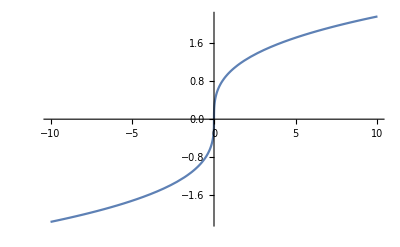

```mathematica
Plot[CubeRoot[x], {x, -10,10}]
```

## 3. Создайте анимацию движения точки по круговой и эллиптической траекториям.

```mathematica
Animate[Show[ParametricPlot[{Sin[x],Cos[x]},{x,0,t+0.01}, PlotRange->{{-1,1},{-1,1}}], Graphics[{Red,PointSize[0.04],Point[{Sin[t],Cos[t]}]},PlotRange->{{-1,1},{-1,1}}]],{t,0,2π}]
```

```mathematica
Animate[Show[ParametricPlot[{Sin[x],2Cos[x]},{x,0,t+0.01}, PlotRange->{{-1,1},{-2,2}}], Graphics[{Red,PointSize[0.04],Point[{Sin[t],2Cos[t]}]},PlotRange->{{-1,1},{-2,2}}]],{t,0,2π}]
```

## 4. Спроектируйте собственные функции.

4.1 Для вычисления факториала для заданного числа.
4.2 Для вычисления двойного факториала заданного числа. 
4.3 Для вычисления n -  ого члена последовательности Фибоначчи. 
4.4 Предложите способ быстрого вычисления n -  ого члена последовательности Фибоначчи.

### 4.1

```mathematica
myFact[0]:=1
myFact[1]:=1
myFact[n_]:=n*myFact[n-1]
```

```mathematica
myFact[5]
```

120

### 4.2

```mathematica
myFact1[0]:=1
myFact1[1]:=1
myFact1[n_]:=n*myFact1[n-2]
```

```mathematica
myFact1[6]
```

48

```mathematica
6!!
```

48

### 4.3

```mathematica
myFib1[1]:=1
```

```mathematica
myFib1[2]:=1
```

```mathematica
myFib1[n_]:=myFib1[n-1]+myFib1[n-2]
```

```mathematica
myFib1[20]
```

6765

```mathematica
Timing[myFib1[20]]
```

{0.015625,6765}

### 4.4

```mathematica
myFib[1]:=1
```

```mathematica
myFib[2]:=1
```

```mathematica
myFib[n_]:=(myFib[n]=myFib[n-1]+myFib[n-2])
```

```mathematica
myFib[20]
```

6765

```mathematica
Timing[myFib[3000]]
```

{0.015625,410615886307971260333568378719267105220125108637369252408885430926905584274113403731330491660850044560830036835706942274588569362145476502674373045446852160486606292497360503469773453733196887405847255290082049086907512622059054542195889758031109222670849274793859539133318371244795543147611073276240066737934085191731810993201706776838934766764778739502174470268627820918553842225858306408301661862900358266857238210235802504351951472997919676524004784236376453347268364152648346245840573214241419937917242918602639810097866942392015404620153818671425739835074851396421139982713640679581178458198658692285968043243656709796000}